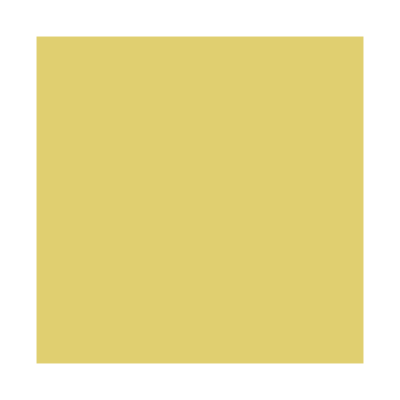

```mathematica
Graphics[{RGBColor[0.88,0.81,0.44],Rectangle[{-0.5,-0.5},{0.5,0.5}]}]
```

```mathematica
g1=Image[%30,ImageSize->18]
```

-Graphics-

```mathematica
g2=SetAlphaChannel[g1,%13]
```

-Graphics-

```mathematica
g2=%14;
```

```mathematica
ImageChannels[g2]
```

4

```mathematica
ImageDimensions[g1]
```

{180,180}

```mathematica
AlphaChannel[g2]
```

-Graphics-

```mathematica
Export["D:\\ProjectNote\\GermaData\\KlickAufDeutschEins\\Ubung\\Button.png",%56,"Image",Background->None]
```

D:\ProjectNote\GermaData\KlickAufDeutschEins\Ubung\Button.png

```mathematica
g3=Import["D:\\ProjectNote\\GermaData\\KlickAufDeutschEins\\Ubung\\Button.png"]
```

-Graphics-

```mathematica
ImageDimensions[g3]
```

{18,19}

```mathematica
ImageDimensions[g1]
```

{18,19}

```mathematica
data=ImageData[g3];
```

```mathematica
data=data[[3;;17,2;;17]]
```

```mathematica
Image[data,ColorSpace->"RGB"]
```

-Graphics-

```mathematica
ImageChannels[%56]
```

4

```mathematica
ImageType[g3]
```

Byte

```mathematica
g3
```

-Graphics-

{{{0.882353,0.811765,0.439216,0.},{0.882353,0.811765,0.439216,0.},{0.882353,0.811765,0.439216,0.},{0.882353,0.811765,0.439216,0.},{0.882353,0.811765,0.439216,0.282353},{0.882353,0.811765,0.439216,0.905882},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,0.937255},{0.882353,0.811765,0.439216,0.376471},{0.882353,0.811765,0.439216,0.},{0.882353,0.811765,0.439216,0.},{0.882353,0.811765,0.439216,0.}},{{0.882353,0.811765,0.439216,0.},{0.882353,0.811765,0.439216,0.},{0.882353,0.811765,0.439216,0.0627451},{0.882353,0.811765,0.439216,0.623529},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,0.717647},{0.882353,0.811765,0.439216,0.0941176},{0.882353,0.811765,0.439216,0.}},{{0.882353,0.811765,0.439216,0.},{0.882353,0.811765,0.439216,0.},{0.882353,0.811765,0.439216,0.623529},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,0.780392},{0.882353,0.811765,0.439216,0.}},{{0.882353,0.811765,0.439216,0.},{0.882353,0.811765,0.439216,0.282353},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,0.501961}},{{0.882353,0.811765,0.439216,0.},{0.882353,0.811765,0.439216,0.905882},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,0.968627}},{{0.882353,0.811765,0.439216,0.156863},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.}},{{0.882353,0.811765,0.439216,0.345098},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.}},{{0.882353,0.811765,0.439216,0.529412},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.}},{{0.882353,0.811765,0.439216,0.407843},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.}},{{0.882353,0.811765,0.439216,0.188235},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.}},{{0.882353,0.811765,0.439216,0.0313725},{0.882353,0.811765,0.439216,0.968627},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.}},{{0.882353,0.811765,0.439216,0.},{0.882353,0.811765,0.439216,0.501961},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,0.654902}},{{0.882353,0.811765,0.439216,0.},{0.882353,0.811765,0.439216,0.0313725},{0.882353,0.811765,0.439216,0.811765},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,0.905882},{0.882353,0.811765,0.439216,0.0941176}},{{0.882353,0.811765,0.439216,0.},{0.882353,0.811765,0.439216,0.},{0.882353,0.811765,0.439216,0.156863},{0.882353,0.811765,0.439216,0.843137},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,0.937255},{0.882353,0.811765,0.439216,0.282353},{0.882353,0.811765,0.439216,0.}},{{0.882353,0.811765,0.439216,0.},{0.882353,0.811765,0.439216,0.},{0.882353,0.811765,0.439216,0.},{0.882353,0.811765,0.439216,0.0313725},{0.882353,0.811765,0.439216,0.623529},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,1.},{0.882353,0.811765,0.439216,0.717647},{0.882353,0.811765,0.439216,0.0941176},{0.882353,0.811765,0.439216,0.},{0.882353,0.811765,0.439216,0.}}}

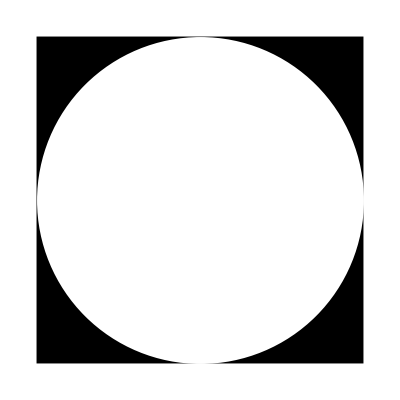

```mathematica
Graphics[{Black,Rectangle[{-0.5,-0.5},{0.5,0.5}],White,Disk[{0,0},0.5]}]
```